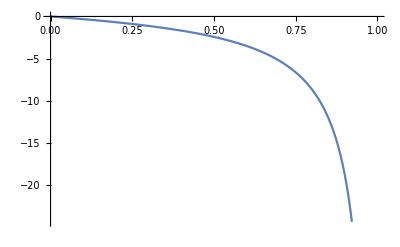

```mathematica
Plot[√( (1-e)/(1+e) )-(1+e)/(1-e),{e,0.00001, 0.999999}]
```

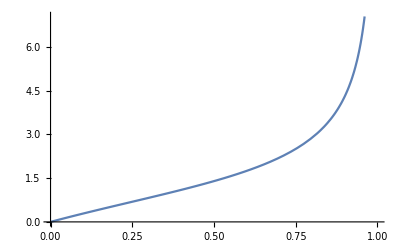

```mathematica
Plot[√( (1+e)/(1-e) )-(1-e)/(1+e),{e,0.00001, 0.999999}]
```

Therefore, it is very clearly visible which is larger, and which is smaller.

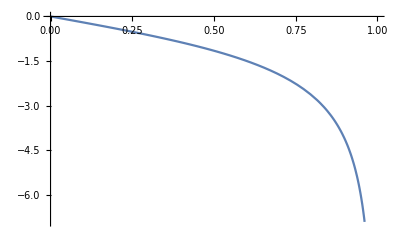

```mathematica
Plot[√( (1-e)/(1+e) )-√((1+e)/(1-e)),{e,0.00001, 0.999999}]
```

```mathematica
Series[√((1+e)/(1-e)),{e, 0, 20}]
```

1+e+e^2/2+e^3/2+(3 e^4)/8+(3 e^5)/8+(5 e^6)/16+(5 e^7)/16+(35 e^8)/128+(35 e^9)/128+(63 e^10)/256+(63 e^11)/256+(231 e^12)/1024+(231 e^13)/1024+(429 e^14)/2048+(429 e^15)/2048+(6435 e^16)/32768+(6435 e^17)/32768+(12155 e^18)/65536+(12155 e^19)/65536+(46189 e^20)/262144+O[e]^21

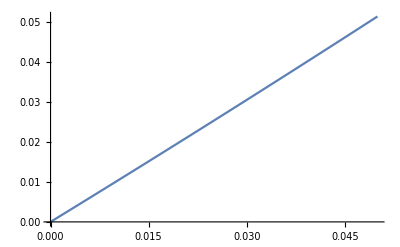

```mathematica
Plot[e+e^2/2+e^3/2+(3 e^4)/8+(3 e^5)/8+(5 e^6)/16+(5 e^7)/16+(35 e^8)/128+(35 e^9)/128+(63 e^10)/256+(63 e^11)/256+(231 e^12)/1024+(231 e^13)/1024+(429 e^14)/2048+(429 e^15)/2048+(6435 e^16)/32768+(6435 e^17)/32768+(12155 e^18)/65536+(12155 e^19)/65536+(46189 e^20)/262144,{e,0.0, 0.05}]
```